data conversion thanks to creidhne, https://mathematica.stackexchange.com/users/41569/creidhne
This Program detects average of stock prices within the customized designed time interval

```mathematica
Clear["Global`*"]
```

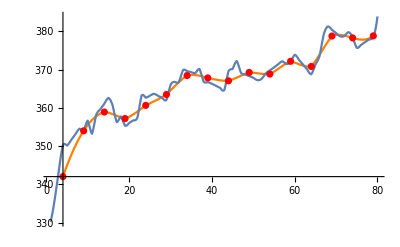

```mathematica
data=FinancialData["NYSE:SPY","Close",{{2020,10,31},{2021,1,22},"Day"},"Value"];
ts=TimeSeries[data,TemporalRegularity->True];
{dt1,dt2}=ts/@{"FirstDate","LastDate"};
dates=DateRange[dt1,dt2];
DateListPlot[Transpose[{dates,ts[dates]}]];


Day=5;
a=QuantityMagnitude[ts[dates]];
n=Length[a];
Avg={};

For[i=1;,i<n-Ceiling[Day/2](*if bugs out do -Ceiling[Day/2]-1 ONLY HERE*),i=i+Day,
Tem=0;
For[j=0,j<Day,j++,
Tem=Tem+a[[i+j]];
];
Tem=Tem/Day;
Avg=Append[Avg,{i+Ceiling[Day/2],Tem}];
]
f=Interpolation[Avg]; 
g=Interpolation[QuantityMagnitude[ts[dates]]];
p1=Plot[f[x],{x,Avg[[1,1]],Avg[[Length[Avg],1]]},PlotStyle->{Orange}];
p2=Plot[g[x],{x,1,Length[ts[dates]]}];
p3=ListPlot[Avg,PlotStyle->Red];
Show[p1,p2,p3,PlotRange-> All]
```

```mathematica
T
```

```mathematica
T
```

```mathematica
Fourier[{{1,1},{2,3}}]
```

{{3.5,-0.5},{-1.5,0.5}}